```mathematica
(* verifies (6, 7) *)
γ=EulerGamma;
μlogm2=Integrate[Log[x^2](4π x^2)/((2π M1D^2)^(3/2))Exp[-x^2/(2 M1D^2)],{x,0,Infinity},Assumptions->{M1D>0}];
Σ=(FullSimplify@Integrate[(Log[x^2]-(2-EulerGamma-Log[2]+2 Log[M1D]))^2(4π x^2)/((2π M1D^2)^(3/2))Exp[-x^2/(2 M1D^2)],{x,0,Infinity},Assumptions->{M1D>0}])^(1/2);
{Simplify[Log[(M1D^2 E^(2-γ))/2]==μlogm2,M1D>0],π^2/2-4==Σ^2}
```

{Log[1/2 ⅇ^(2-EulerGamma) M1D^2]==2-EulerGamma-Log[2]+2 Log[M1D],True}

```mathematica
(* verifies (9) *)
expr9=Integrate[Exp[I ω ((Log[x^2]-(μlogm2))/(√n Σ))](4π x^2)/((2π M1D^2)^(3/2))Exp[-x^2/(2 M1D^2)],{x,0,Infinity},Assumptions->{M1D>0,n>0}];
ϕ[ω_,n_]:=(4 E^(EulerGamma-2))^(ⅈ √n ω/Σ) (2/(√π)Gamma[3/2+(ⅈ ω)/(√n Σ)])^n;
Simplify[expr9^n/ϕ[ω,n],{Element[n,Integers],n≥1}]
```

```mathematica
Simplify[expr9^n/ϕ[ω,n],{Element[n,Integers],n≥1,Element[ω,Reals]||Im[ω]<0}]
```

ConditionalExpression[1, ω∈ℝ||Im[ω]<0||9 n (-8+π^2)>8 Im[ω]^2]

```mathematica
(* loads up pre-tabulated (10) for various n. If specific n can't be found, loads up next available. *)
SetDirectory[NotebookDirectory[]];
fTilted[s_,n_?NumericQ]:=1/(2π)Re@Quiet@NIntegrate[E^(-I ω s)ϕ[ω,n],{ω,-Infinity,Infinity},MaxRecursion->1000,WorkingPrecision->50,PrecisionGoal->40];
flogρN[μ_,σ_,n_]:=Module[{fit,m},
m=Round@Abs@n;
While[!FileExistsQ["sfit\\"<>ToString[m]<>".txt"],m++];
fit=Import["sfit\\"<>ToString[m]<>".txt","Table"];
If[n>0,fit=Transpose@{σ fit[[;;,1]]+μ,1/σ fit[[;;,2]]},fit=Transpose@{-σ fit[[;;,1]]+μ,1/σ fit[[;;,2]]}];
Interpolation[fit]
];
nest[μ_,σ_]:=((0.4585 σ^3)/(3(1-E^(-μ-σ^2/2))))^2;
nestPrecisep[μ_,σ_]:=Re[x/.FindRoot[E^μ ϕ[-I σ,x]==1,{x,10}]];
norm[μ_,σ_,n_]:=E^μ ϕ[-I σ,n];
fln[x_,σ_]:=1/(√(2π σ^2))Exp[-((x+σ^2/2)^2)/(2 σ^2)];
fln[x_,μ_,σ_]:=1/(√(2π σ^2))Exp[-(x-μ)^2/(2 σ^2)];
```

```mathematica
sdataInterp
```

InterpolatingFunction[…]

```mathematica
SetDirectory[NotebookDirectory[]];
dirs={"mach1","mach2.5","mach5","mach10","mach20","mach40","mach80","mach160","mach320"};
stats={};
fitpars={};
εln={};
εest={};
εest2={};
εfit={};
Monitor[For[i=1,i≤Length@dirs,i++,
prefix=dirs[[i]];
AppendTo[stats,Import[prefix<>"//"<>prefix<>"_Pearson_stat.txt","Table"]];
AppendTo[fitpars,First@Import[prefix<>"//"<>prefix<>"_logrho_fitpars_preserving_V_1e-3.txt","Table"]];
cdf=Import[prefix<>"//"<>prefix<>"_logrho_CDF_map_frames_20-300_V_1e-3.txt","Table"];
cdf=Select[cdf,First@#>0.01&];
sdata=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"];
sdata=Select[sdata,Last@#>cdf[[1,2]]&];
sdataInterp=Interpolation[Transpose@{0.5(sdata[[;;,1]]+sdata[[;;,2]]),sdata[[;;,4]]}];
ymax=Max[sdata[[;;,4]]];
sest=flogρN[stats[[i,1,2]],stats[[i,2,2]],nest[stats[[i,1,2]],stats[[i,2,2]]]];
sfit=flogρN[Log[1/ϕ[-I fitpars[[i,1]],Round[1/fitpars[[i,2]]]]],fitpars[[i,1]],Round[1/fitpars[[i,2]]]];
fitln=NonlinearModelFit[Transpose@{0.5(sdata[[;;,1]]+sdata[[;;,2]]),sdata[[;;,4]]},{fln[x,σ],σ>0},{{σ,fitpars[[i,2]]}},x];

AppendTo[εln,(Quiet@NIntegrate[Abs[fitln[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}])];
AppendTo[εfit,(Quiet@NIntegrate[Abs[sfit[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}])];
AppendTo[εest,(Quiet@NIntegrate[Abs[sest[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}])];
Print[E^(μ+σ^2/2)/.fitln[[1,2]]];
],i]
```

ⅇ^(0.0000711003+μ)

ⅇ^(0.00212017+μ)

ⅇ^(0.0224786+μ)

ⅇ^(0.148451+μ)

ⅇ^(0.479488+μ)

ⅇ^(0.943873+μ)

ⅇ^(1.34227+μ)

ⅇ^(1.51179+μ)

ⅇ^(1.59933+μ)

```mathematica
Mnom={0.1,0.25,0.5,1,2,4,8,16,32};
tabFull=Table[{SetPrecision[Mnom[[i]],3],SetPrecision[stats[[i,4,2]],3],-SetPrecision[stats[[i,1,2]],3],SetPrecision[stats[[i,2,2]],3],ToString[Round@nest[stats[[i,1,2]],stats[[i,2,2]]]]<>" ("<>ToString[Round@nestPrecisep[stats[[i,1,2]],stats[[i,2,2]]]]<>")",-SetPrecision[fitpars[[i,1]],3],SetPrecision[fitpars[[i,2]],3],Round[1/fitpars[[i,3]]],SetPrecision[norm[fitpars[[i,1]],fitpars[[i,2]],Abs@Round[1/fitpars[[i,3]]]],2],SetPrecision[100εln[[i]],3],ToString[SetPrecision[100εest[[i]],3]]<>" ("<>ToString[SetPrecision[100εest2[[i]],3]]<>")",SetPrecision[100εfit[[i]],3]},{i,1,Length@stats}];
tab=Table[{SetPrecision[Mnom[[i]],3],SetPrecision[stats[[i,4,2]],3],-SetPrecision[stats[[i,1,2]],3],SetPrecision[stats[[i,2,2]],3],ToString[Round@nest[stats[[i,1,2]],stats[[i,2,2]]]],-SetPrecision[Re@Log[1/ϕ[-I fitpars[[i,1]],Round[1/fitpars[[i,2]]]]],3],SetPrecision[fitpars[[i,1]],3],Round[1/fitpars[[i,2]]],SetPrecision[100εln[[i]],3],ToString[SetPrecision[100εest[[i]],3]],SetPrecision[100εfit[[i]],3]},{i,1,Length@stats}];
PrependTo[tab,{"M_(1  D)","M_(1  D)","-μ_(est.)","σ_(est.)","n_(est.)","-μ_fit","σ_fit","n_fit","ε_ln(%)","ε_(est.)(%)","ε_fit(%)"}];
tab//MatrixForm
```

Part::partw: Part 3 of {0.0119924,0.0432142} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

(M_(1  D) | M_(1  D) | -μ_(est.) | σ_(est.) | n_(est.) | -μ_fit | σ_fit | n_fit | ε_ln(%) | ε_(est.)(%) | ε_fit(%)
0.1 | 0.0946 | 0.0000789 | 0.0126 | 15 | 0.0000719 | 0.012 | 23 | 4.37 | 4.69 | 2.39
0.25 | 0.239 | 0.00233 | 0.0686 | 8 | 0.00214 | 0.0656 | 22 | 4.84 | 4.59 | 1.92
0.5 | 0.474 | 0.0245 | 0.224 | 9 | 0.0229 | 0.216 | 11 | 6.31 | 3.38 | 1.77
1. | 0.899 | 0.152 | 0.559 | 33 | 0.151 | 0.558 | 26 | 4.14 | 0.747 | 0.464
2. | 1.67 | 0.479 | 0.998 | 59 | 0.482 | 1. | 58 | 3.4 | 0.518 | 0.435
4. | 3.21 | 0.951 | 1.43 | 36 | 0.956 | 1.44 | 27 | 5.24 | 0.412 | 0.254
8. | 6.38 | 1.36 | 1.76 | 24 | 1.37 | 1.76 | 15 | 7.51 | 1.14 | 0.341
16. | 12.9 | 1.57 | 1.94 | 17 | 1.56 | 1.92 | 9 | 10.1 | 2.79 | 0.617
32. | 25.6 | 1.7 | 2.08 | 14 | 1.65 | 2.03 | 5 | 12.5 | 5.21 | 1.37)

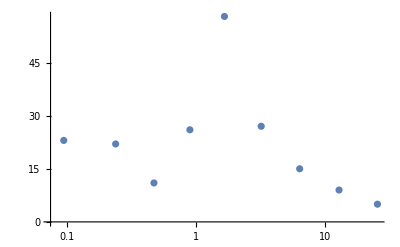

```mathematica
ListLogLinearPlot@Transpose@{tab[[2;;,2]],tab[[2;;,8]]}
```

```mathematica
prefixes={"mach1","mach2.5","mach5","mach10","mach20"};
goodFitCol=RGBColor[0.845274, 0.369528, 0.19115];
badFitCol=RGBColor[0.04, 0.56, 1.];
const=(2 √2(-8+7 Zeta[3]))/((-8+π^2)^(3/2));imgSize=Automatic;
noTic=Directive[FontOpacity->0,FontSize->0];
dec[x_,n_]:=n-Ceiling@Log10@Abs[x];
grid={{},{}};
Monitor[
For[k=1,k≤4,k++,
prefix=prefixes[[k]];
If[FileExistsQ["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"\\"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt"],
data=Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"\\"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"],
data=Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"\\"<>prefix<>"_logrho_bins_frames_20-199_V_1e-3.txt","Table"];
];
data2=Transpose@{0.5(data[[;;,1]]+data[[;;,2]]),data[[;;,4]]};
params=First@Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"\\"<>prefix<>"_logrho_fitpars_V_1e-3.txt","Table"];
stats=Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"//"<>prefix<>"_Pearson_stat.txt","Table"];
If[FileExistsQ[
prefix<>"//"<>prefix<>"_logrho_CDF_map_frames_20-300_V_1e-3.txt"],
cdf=Import[prefix<>"//"<>prefix<>"_logrho_CDF_map_frames_20-300_V_1e-3.txt","Table"],
cdf=Import[prefix<>"//"<>prefix<>"_logrho_CDF_map_frames_20-199_V_1e-3.txt","Table"]
];
cdf=Select[cdf,First@#>0.01&];
If[FileExistsQ[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt"],
sdata=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"],
sdata=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-199_V_1e-3.txt","Table"]
];
sdata=Select[sdata,Last@#>cdf[[1,2]]&];
xmin=params[[1]]-4params[[2]];
xmax=params[[1]]+4params[[2]];
indexmax=OrderingBy[data2,Last][[-1]];
ymax=data2[[indexmax,2]];
x0=data2[[indexmax,1]];
dataL=Select[data2[[;;indexmax]],First@#≥xmin&];
dataR=Select[data2[[indexmax;;]],First@#≤xmax&];
ymin =Min[dataL[[1,2]],dataR[[-1,2]]];
dx=xmax-xmin;
dy=ymax/ymin;
data={};
AppendTo[data,{x0,ymax}];
ds=0;
For[i=Length@dataL-1,i≥1,i--,
ds+=√(((dataL[[i,1]]-dataL[[i+1,1]])/xmax)^2+(Log[dataL[[i,2]]/dataL[[i+1,2]]]/Log[ymax/ymin])^2);
If[ds≥0.03,
PrependTo[data,dataL[[i]]];
ds=0;
];
];
ds=0;
For[i=2,i≤Length@dataR,i++,
ds+=√(((dataR[[i,1]]-dataR[[i-1,1]])/xmax)^2+(Log[dataR[[i,2]]/dataR[[i-1,2]]]/Log[ymax/ymin])^2);
If[ds≥0.03,
AppendTo[data,dataR[[i]]];
ds=0;
];
];
napprox=Round[nest[stats[[1,2]],stats[[2,2]]]];
fitLN=NonlinearModelFit[data,1/(√(2π s^2))Exp[-(x-μ)^2/(2 s^2)],{s,μ},x];
If[FileExistsQ[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt"],
dataErr=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"],
dataErr=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-199_V_1e-3.txt","Table"]
];
dataErr=Transpose@{0.5(dataErr[[;;,1]]+dataErr[[;;,2]]),dataErr[[;;,4]]};
sdataInterp=Interpolation[dataErr];
sest=flogρN[stats[[1,2]],stats[[2,2]],nest[stats[[1,2]],stats[[2,2]]]];
sest2=flogρN[stats[[1,2]],stats[[2,2]],nestPrecisep[stats[[1,2]],stats[[2,2]]]];
sfit=flogρN[params[[1]],params[[2]],1/params[[3]]];
fitln=NonlinearModelFit[Transpose@{0.5(sdata[[;;,1]]+sdata[[;;,2]]),sdata[[;;,4]]},{fln[x,σ],σ>0},{{σ,params[[2]]}},x];

LNErr=(Quiet@NIntegrate[Abs[fitln[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
absErr=(Quiet@NIntegrate[Abs[sfit[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
estErr=(Quiet@NIntegrate[Abs[sest[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
estErr2=(Quiet@NIntegrate[Abs[sest2[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
ticks=Ticks/.AbsoluteOptions@ListLogPlot[data,PlotRange->{{xmin-0.1dx,xmax+0.1dx},{3 10^-5,20}}];
ticks2=Ticks/.AbsoluteOptions@LogPlot[Abs[(fun1[x]-fun2[x])/fun1[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{10^-6,10}}];
ticks[[2,;;,1]]=Exp[ticks[[2,;;,1]]];
ticks2[[2,;;,1]]=Exp[ticks2[[2,;;,1]]];
ticksTR=SortBy[ticks[[2]],First][[2;;-2]];
ticksBR=SortBy[ticks2[[2]],First][[2;;-2]];
ticks[[1,;;,3,2]]=ticks[[1,;;,3,1]];
ticks[[2,;;,3,2]]=ticks[[2,;;,3,1]];
ticks2[[1,;;,3,2]]=ticks2[[1,;;,3,1]];
ticks2[[2,;;,3,2]]=ticks2[[2,;;,3,1]];
ticksBT=SortBy[ticks[[1]],First][[2;;-2]];
ticksTLR=SortBy[ticks[[2]],First][[2;;-2]];
ticksBLR=SortBy[ticks2[[2]],First][[2;;-3]];
M1D=stats[[4,2]];FWHML=sdata[[1,1]];FWHMH=sdata[[-1,2]];
μfit=SetPrecision[params[[1]],3];
σfit=SetPrecision[params[[2]],3];
nfit=Round[1/params[[3]]];
epilogT={Text[Style["M_(1  D) = "<>ToString[NumberForm[M1D,{3,dec[M1D,3]}]],Black,13,TextAlignment->Left],Scaled[{0.3605,0.45}],{-1,0}],Text[Style["μ = "<>ToString[NumberForm[μfit,{3,dec[μfit,3]}]],Black,13,TextAlignment->Left],Scaled[{0.421,0.35}],{-1,0}],Text[Style["σ = "<>ToString[NumberForm[σfit,{3,dec[σfit,3]}]],Black,13,TextAlignment->Left],Scaled[{0.418,0.25}],{-1,0}],Text[Style["n = "<>ToString[nfit],Black,13,TextAlignment->Left],Scaled[{0.421,0.15}],{-1,0}]};
epilogB={Text[Style["LN err: "<>ToString[NumberForm[100LNErr,{3,dec[100LNErr,2]}]]<>"%",Black,13,TextAlignment->Left],Scaled[{0.5,0.88}],{0,0}],Text[Style["fit err: "<>ToString[NumberForm[100absErr,{3,dec[100absErr,2]}]]<>"%",Black,13,TextAlignment->Left],Scaled[{0.5,0.78}],{0,0}],{Dashed,Black,Line[{{FWHML,-20},{FWHML,1}}]},{Dashed,Black,Line[{{FWHMH,-20},{FWHMH,1}}]}};
Which[k==1,pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{10^-5,30}},Axes->False,Frame->{{True,False},{True,True}},FrameTicks->{{Automatic,None},{ticksBT,Automatic}},FrameTicksStyle->{{Automatic,noTic},{noTic,noTic}},ImagePadding->{{Automatic,None},{None,None}},FrameLabel->{{Style["f(s; μ, σ, n)",Black,12],None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,None},{None,None}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{10^-6,30}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->{{Automatic,noTic},{Automatic,noTic}},FrameLabel->{{Style["abs. error",Black,12],None},{None,None}},AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{None,None},{None,None}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]];
,
(k==2)||(k==3),
pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{10^-5,30}},Axes->False,FrameTicks->{{ticksTLR,None},{ticksBT,Automatic}},Frame->{{True,False},{True,True}},FrameTicksStyle->{{noTic,noTic},{noTic,noTic}},ImagePadding->{{Automatic,None},{None,None}},FrameLabel->{{None,None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,None},{Automatic,None}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{10^-6,30}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,False},{True,False}},FrameTicks->{{ticksBLR,None},{Automatic,None}},FrameTicksStyle->{{noTic,noTic},{Automatic,noTic}},FrameLabel->None,AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{None,None},{Automatic,None}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]],
k==4,
pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{10^-5,30}},Axes->False,Frame->{{True,True},{True,True}},FrameTicks->{{ticksTLR,ticksTR},{ticksBT,Automatic}},FrameTicksStyle->{{noTic,noTic},{noTic,noTic}},FrameLabel->{{None,None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{10^-6,30}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,True},{True,False}},FrameTicks->{{ticksBLR,ticksBR},{Automatic,None}},FrameTicksStyle->{{noTic,noTic},{Automatic,noTic}},FrameLabel->None,AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]];
];
AppendTo[grid[[1]],pTop];
AppendTo[grid[[2]],pBot];
],k]
Export["H:\\scratch\\projects\\Mach_grid_256\\img\\logrho_V_top_row_pics_abs_error_new.pdf",Labeled[GraphicsGrid[grid,Spacings->{-65.6,-39.4},ImageSize->1200],"s = log(ρ)",Bottom,LabelStyle->Directive[FontFamily->"Arial",FontSize->12],Spacings->{0,-0.2}],ImageSize->1200];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
prefixes={"mach40_low_PPM","mach80","mach160","mach320"};
goodFitCol=RGBColor[0.845274, 0.369528, 0.19115];
badFitCol=RGBColor[0.04, 0.56, 1.];
const=(2 √2(-8+7 Zeta[3]))/((-8+π^2)^(3/2));imgSize=Automatic;
noTic=Directive[FontOpacity->0,FontSize->0];
dec[x_,n_]:=n-Ceiling@Log10@Abs[x];
grid={{},{}};
Monitor[
For[k=1,k≤4,k++,
prefix=prefixes[[k]];
data=Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"\\"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"];
data2=Transpose@{0.5(data[[;;,1]]+data[[;;,2]]),data[[;;,4]]};
params=First@Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"\\"<>prefix<>"_logrho_fitpars_V_1e-3.txt","Table"];
stats=Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"//"<>prefix<>"_Pearson_stat.txt","Table"];
cdf=Import[prefix<>"//"<>prefix<>"_logrho_CDF_map_frames_20-300_V_1e-3.txt","Table"];
cdf=Select[cdf,First@#>0.01&];
sdata=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"];
sdata=Select[sdata,Last@#>cdf[[1,2]]&];
xmin=params[[1]]-4params[[2]];
xmax=params[[1]]+4params[[2]];
indexmax=OrderingBy[data2,Last][[-1]];
ymax=data2[[indexmax,2]];
x0=data2[[indexmax,1]];
dataL=Select[data2[[;;indexmax]],First@#≥xmin&];
dataR=Select[data2[[indexmax;;]],First@#≤xmax&];
ymin =Min[dataL[[1,2]],dataR[[-1,2]]];
dx=xmax-xmin;
dy=ymax/ymin;
data={};
AppendTo[data,{x0,ymax}];
ds=0;
For[i=Length@dataL-1,i≥1,i--,
ds+=√(((dataL[[i,1]]-dataL[[i+1,1]])/xmax)^2+(Log[dataL[[i,2]]/dataL[[i+1,2]]]/Log[ymax/ymin])^2);
If[ds≥0.03,
PrependTo[data,dataL[[i]]];
ds=0;
];
];
ds=0;
For[i=2,i≤Length@dataR,i++,
ds+=√(((dataR[[i,1]]-dataR[[i-1,1]])/xmax)^2+(Log[dataR[[i,2]]/dataR[[i-1,2]]]/Log[ymax/ymin])^2);
If[ds≥0.03,
AppendTo[data,dataR[[i]]];
ds=0;
];
];
napprox=Round[nest[stats[[1,2]],stats[[2,2]]]];
fitLN=NonlinearModelFit[data,1/(√(2π s^2))Exp[-(x-μ)^2/(2 s^2)],{s,μ},x];
dataErr=Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"\\"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"];
dataErr=Transpose@{0.5(dataErr[[;;,1]]+dataErr[[;;,2]]),dataErr[[;;,4]]};
sdataInterp=Interpolation[dataErr];
sest=flogρN[stats[[1,2]],stats[[2,2]],nest[stats[[1,2]],stats[[2,2]]]];
sest2=flogρN[stats[[1,2]],stats[[2,2]],nestPrecisep[stats[[1,2]],stats[[2,2]]]];
sfit=flogρN[params[[1]],params[[2]],1/params[[3]]];
fitln=NonlinearModelFit[Transpose@{0.5(sdata[[;;,1]]+sdata[[;;,2]]),sdata[[;;,4]]},{fln[x,σ],σ>0},{{σ,params[[2]]}},x];

LNErr=(Quiet@NIntegrate[Abs[fitln[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
absErr=(Quiet@NIntegrate[Abs[sfit[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
estErr=(Quiet@NIntegrate[Abs[sest[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
estErr2=(Quiet@NIntegrate[Abs[sest2[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
ymaxTop=5;yminTop=10^-4;
ymaxBot=10;yminBot=5 10^-7;
ticks=Ticks/.AbsoluteOptions@ListLogPlot[data,PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminTop,ymaxTop}}];
ticks2=Ticks/.AbsoluteOptions@LogPlot[Abs[(fun1[x]-fun2[x])/fun1[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminBot,ymaxBot}}];
ticks[[2,;;,1]]=Exp[ticks[[2,;;,1]]];
ticks2[[2,;;,1]]=Exp[ticks2[[2,;;,1]]];
ticksTR=SortBy[ticks[[2]],First][[2;;-2]];
ticksBR=SortBy[ticks2[[2]],First][[2;;-2]];
ticks[[1,;;,3,2]]=ticks[[1,;;,3,1]];
ticks[[2,;;,3,2]]=ticks[[2,;;,3,1]];
ticks2[[1,;;,3,2]]=ticks2[[1,;;,3,1]];
ticks2[[2,;;,3,2]]=ticks2[[2,;;,3,1]];
ticksBT=SortBy[ticks[[1]],First][[2;;-2]];
ticksTLR=SortBy[ticks[[2]],First][[2;;-2]];
ticksBLR=SortBy[ticks2[[2]],First][[2;;-3]];
M1D=stats[[4,2]];FWHML=sdata[[1,1]];FWHMH=sdata[[-1,2]];
μfit=SetPrecision[params[[1]],3];
σfit=SetPrecision[params[[2]],3];
nfit=Round[1/params[[3]]];
epilogT={Text[Style["M_(1  D) = "<>ToString[NumberForm[M1D,{3,dec[M1D,3]}]],Black,13,TextAlignment->Left],Scaled[{0.3605,0.45}],{-1,0}],Text[Style["μ = "<>ToString[NumberForm[μfit,{3,dec[μfit,3]}]],Black,13,TextAlignment->Left],Scaled[{0.421,0.35}],{-1,0}],Text[Style["σ = "<>ToString[NumberForm[σfit,{3,dec[σfit,3]}]],Black,13,TextAlignment->Left],Scaled[{0.418,0.25}],{-1,0}],Text[Style["n = "<>ToString[nfit],Black,13,TextAlignment->Left],Scaled[{0.421,0.15}],{-1,0}]};
epilogB={Text[Style["LN err: "<>ToString[NumberForm[100LNErr,{3,dec[100LNErr,2]}]]<>"%",Black,13,TextAlignment->Left],Scaled[{0.5,0.88}],{0,0}],Text[Style["fit err: "<>ToString[NumberForm[100absErr,{3,dec[100absErr,2]}]]<>"%",Black,13,TextAlignment->Left],Scaled[{0.5,0.78}],{0,0}],{Dashed,Black,Line[{{FWHML,-20},{FWHML,1}}]},{Dashed,Black,Line[{{FWHMH,-20},{FWHMH,1}}]}};
Which[k==1,pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminTop,ymaxTop}},Axes->False,Frame->{{True,False},{True,True}},FrameTicks->{{Automatic,None},{ticksBT,Automatic}},FrameTicksStyle->{{Automatic,noTic},{noTic,noTic}},ImagePadding->{{Automatic,None},{None,None}},FrameLabel->{{Style["f(s; μ, σ, n)",Black,12],None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,None},{None,None}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminBot,ymaxBot}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->{{Automatic,noTic},{Automatic,noTic}},FrameLabel->{{Style["abs. error",Black,12],None},{None,None}},AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{None,None},{None,None}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]];
,
(k==2)||(k==3),
pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminTop,ymaxTop}},Axes->False,FrameTicks->{{ticksTLR,None},{ticksBT,Automatic}},Frame->{{True,False},{True,True}},FrameTicksStyle->{{noTic,noTic},{noTic,noTic}},ImagePadding->{{Automatic,None},{None,None}},FrameLabel->{{None,None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,None},{Automatic,None}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminBot,ymaxBot}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,False},{True,False}},FrameTicks->{{ticksBLR,None},{Automatic,None}},FrameTicksStyle->{{noTic,noTic},{Automatic,noTic}},FrameLabel->None,AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{None,None},{Automatic,None}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]],
k==4,
pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminTop,ymaxTop}},Axes->False,Frame->{{True,True},{True,True}},FrameTicks->{{ticksTLR,ticksTR},{ticksBT,Automatic}},FrameTicksStyle->{{noTic,noTic},{noTic,noTic}},FrameLabel->{{None,None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminBot,ymaxBot}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,True},{True,False}},FrameTicks->{{ticksBLR,ticksBR},{Automatic,None}},FrameTicksStyle->{{noTic,noTic},{Automatic,noTic}},FrameLabel->None,AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]];
];
AppendTo[grid[[1]],pTop];
AppendTo[grid[[2]],pBot];
],k]
Export["H:\\scratch\\projects\\Mach_grid_256\\img\\logrho_V_bottom_row_pics_abs_error_new.pdf",Labeled[GraphicsGrid[grid,Spacings->{-65.6,-39.4},ImageSize->1200],"s = log(ρ)",Bottom,LabelStyle->Directive[FontFamily->"Arial",FontSize->12],Spacings->{0,-0.2}],ImageSize->1200];
```

InterpolatingFunction::dmval: Input value {-6.70201} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
s={};
i=2;
For[i=2,i≤Length[tab],i++,
For[j=1,j≤Length[tab[[i]]]-1,j++,
s=s<>ToString[tab[[i]][[j]]]<>" & ";
];
s=s<>ToString[tab[[i]][[j]]]<>" \\\\ \n";
]
s
```

0.100 & 0.0958 & 0.00113 & 0.0475 & 46 & 0.00112 & 0.0475 & -45 & 1.00 & 3.09 & 6.14 & 0.0645 \\ 
0.250 & 0.239 & 0.00233 & 0.0686 & 8 & 0.00152 & 0.0655 & 27 & 1.00 & 4.84 & 4.59 & 1.88 \\ 
0.500 & 0.472 & 0.0244 & 0.223 & 11 & 0.0234 & 0.216 & 15 & 1.0 & 5.53 & 3.03 & 1.50 \\ 
1.00 & 0.892 & 0.153 & 0.561 & 38 & 0.155 & 0.559 & 23 & 1.0 & 4.03 & 0.833 & 0.305 \\ 
2.00 & 1.67 & 0.479 & 0.998 & 59 & 0.477 & 1.00 & 69 & 1.01 & 3.40 & 0.518 & 0.324 \\ 
4.00 & 3.21 & 0.951 & 1.43 & 36 & 0.950 & 1.44 & 31 & 1.01 & 5.24 & 0.412 & 0.162 \\ 
8.00 & 6.38 & 1.36 & 1.76 & 24 & 1.36 & 1.76 & 16 & 1.01 & 7.51 & 1.14 & 0.210 \\ 
16.0 & 12.9 & 1.57 & 1.94 & 17 & 1.55 & 1.92 & 9 & 1.00 & 10.1 & 2.79 & 0.608 \\ 
32.0 & 25.6 & 1.70 & 2.08 & 14 & 1.67 & 2.03 & 5 & 0.98 & 12.5 & 5.21 & 1.13 \\

```mathematica
SetDirectory[NotebookDirectory[]];
prefixes={"mach1","mach2.5","mach5"};
fontSizeTicks=11;
fontSizeLabels=18;
fontSizeParams=16;
ClearAll[s];
goodFitCol=RGBColor[0.845274, 0.369528, 0.19115];
badFitCol=RGBColor[0.04, 0.56, 1.];
const=(2 √2(-8+7 Zeta[3]))/((-8+π^2)^(3/2));imgSize=Automatic;
noTic=Directive[FontOpacity->0,FontSize->0];
dec[x_,n_]:=n-Ceiling@Log10@Abs[x];
grid={{},{}};
Monitor[
For[k=1,k≤3,k++,
prefix=prefixes[[k]];
data=Import[prefix<>"\\"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"];
data2=Transpose@{0.5(data[[;;,1]]+data[[;;,2]]),data[[;;,4]]};
params=First@Import[prefix<>"\\"<>prefix<>"_logrho_fitpars_preserving_V_1e-3.txt","Table"];
stats=Import[prefix<>"//"<>prefix<>"_Pearson_stat.txt","Table"];
cdf=Import[prefix<>"//"<>prefix<>"_logrho_CDF_map_frames_20-300_V_1e-3.txt","Table"];
cdf=Select[cdf,First@#>0.01&];
sdata=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"];
sdata=Select[sdata,Last@#>cdf[[1,2]]&];
xmin=sdata[[1,1]];
xmax=sdata[[-1,2]];
indexmax=OrderingBy[data2,Last][[-1]];
ymax=data2[[indexmax,2]];
x0=data2[[indexmax,1]];
dataL=Select[data2[[;;indexmax]],First@#≥xmin&];
dataR=Select[data2[[indexmax;;]],First@#≤xmax&];
ymin =Min[dataL[[1,2]],dataR[[-1,2]]];
dx=xmax-xmin;
dy=ymax/ymin;
data={};
AppendTo[data,{x0,ymax}];
ds=0;
For[i=Length@dataL-1,i≥1,i--,
ds+=√(((dataL[[i,1]]-dataL[[i+1,1]])/xmax)^2+(Log[dataL[[i,2]]/dataL[[i+1,2]]]/Log[ymax/ymin])^2);
If[ds≥0.03,
PrependTo[data,dataL[[i]]];
ds=0;
];
];
ds=0;
For[i=2,i≤Length@dataR,i++,
ds+=√(((dataR[[i,1]]-dataR[[i-1,1]])/xmax)^2+(Log[dataR[[i,2]]/dataR[[i-1,2]]]/Log[ymax/ymin])^2);
If[ds≥0.03,
AppendTo[data,dataR[[i]]];
ds=0;
];
];
napprox=Round[nest[stats[[1,2]],stats[[2,2]]]];
fitLN=NonlinearModelFit[data,1/(√(2π s^2))Exp[-(x-μ)^2/(2 s^2)],{s,μ},x];
dataErr=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"];
dataErr=Transpose@{0.5(dataErr[[;;,1]]+dataErr[[;;,2]]),dataErr[[;;,4]]};
sdataInterp=Interpolation[dataErr];
sest=flogρN[stats[[1,2]],stats[[2,2]],nest[stats[[1,2]],stats[[2,2]]]];
sest2=flogρN[stats[[1,2]],stats[[2,2]],nestPrecisep[stats[[1,2]],stats[[2,2]]]];
sfit=flogρN[Re@Log[1/ϕ[-I params[[1]],Round[1/params[[2]]]]],params[[1]],1/params[[2]]];
fitln=NonlinearModelFit[Transpose@{0.5(sdata[[;;,1]]+sdata[[;;,2]]),sdata[[;;,4]]},{fln[x,σ],σ>0},{{σ,params[[1]]}},x];

LNErr=(Quiet@NIntegrate[Abs[fitln[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
absErr=(Quiet@NIntegrate[Abs[sfit[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
estErr=(Quiet@NIntegrate[Abs[sest[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
estErr2=(Quiet@NIntegrate[Abs[sest2[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
yminT=0.008;ymaxT=100;
yminB=10^-4;ymaxB=50;
ticks=Ticks/.AbsoluteOptions@ListLogPlot[data,PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminT,ymaxT}}];
ticks2=Ticks/.AbsoluteOptions@LogPlot[Abs[(fun1[x]-fun2[x])/fun1[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminB,ymaxB}}];
ticks[[2,;;,1]]=Exp[ticks[[2,;;,1]]];
ticks2[[2,;;,1]]=Exp[ticks2[[2,;;,1]]];
ticksTR=SortBy[ticks[[2]],First][[2;;-2]];
ticksBR=SortBy[ticks2[[2]],First][[2;;-2]];
ticks[[1,;;,3,2]]=ticks[[1,;;,3,1]];
ticks[[2,;;,3,2]]=ticks[[2,;;,3,1]];
ticks2[[1,;;,3,2]]=ticks2[[1,;;,3,1]];
ticks2[[2,;;,3,2]]=ticks2[[2,;;,3,1]];
ticksBT=SortBy[ticks[[1]],First][[2;;-2]];
ticksTLR=SortBy[ticks[[2]],First][[2;;-2]];
ticksBLR=SortBy[ticks2[[2]],First][[2;;-3]];
M1D=stats[[4,2]];FWHML=sdata[[1,1]];FWHMH=sdata[[-1,2]];
μfit=SetPrecision[Re@Log[1/ϕ[-I params[[1]],Round[1/params[[2]]]]],3];
σfit=SetPrecision[params[[1]],3];
nfit=Round[1/params[[2]]];
epilogT=Inset[Column[{Style["M_(1  D) = "<>ToString[SetPrecision[M1D,3]],Black,fontSizeParams],Style["μ = "<>ToString[SetPrecision[μfit,3]],Black,fontSizeParams],Style["σ = "<>ToString[SetPrecision[σfit,3]],Black,fontSizeParams],Style["n = "<>ToString[nfit],Black,fontSizeParams]},"=",Spacings->{Automatic,0.8}],Scaled@{0.5,0.35}];
epilogB={Inset[Column[{Style["LN err: "<>ToString[SetPrecision[100LNErr,3]]<>"%",Black,fontSizeParams],Style["fit err: "<>ToString[SetPrecision[100absErr,3]]<>"%",Black,fontSizeParams]},":",Spacings->{Automatic,0.8}],Scaled@{0.5,0.82}],{Dashed,Black,Line[{{FWHML,Log@yminB},{FWHML,Log@ymaxB}}]},{Dashed,Black,Line[{{FWHMH,Log@yminB},{FWHMH,Log@ymaxB}}]}};
Which[k==1,pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminT,ymaxT}},Axes->False,Frame->{{True,False},{True,True}},FrameTicks->{{Automatic,None},{ticksBT,Automatic}},FrameTicksStyle->{{{Black,fontSizeTicks},noTic},{noTic,noTic}},ImagePadding->{{Automatic,None},{None,None}},FrameLabel->{{Style["f(s; μ, σ, n)",Black,fontSizeLabels],None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,None},{None,20}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminB,ymaxB}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->{{{Black,fontSizeTicks},noTic},{{Black,fontSizeTicks},noTic}},FrameLabel->{{Style["abs. error",Black,fontSizeLabels],None},{None,None}},AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{None,None},{None,None}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]];
,
(k==2),
pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminT,ymaxT}},Axes->False,FrameTicks->{{ticksTLR,None},{ticksBT,Automatic}},Frame->{{True,False},{True,True}},FrameTicksStyle->{{noTic,noTic},{noTic,noTic}},ImagePadding->{{Automatic,None},{None,None}},FrameLabel->{{None,None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,None},{Automatic,20}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminB,ymaxB}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,False},{True,False}},FrameTicks->{{ticksBLR,None},{Automatic,None}},FrameTicksStyle->{{noTic,noTic},{{Black,fontSizeTicks},noTic}},FrameLabel->None,AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{None,None},{Automatic,None}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]],
k==3,
pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminT,ymaxT}},Axes->False,Frame->{{True,True},{True,True}},FrameTicks->{{ticksTLR,ticksTR},{ticksBT,Automatic}},FrameTicksStyle->{{noTic,noTic},{noTic,noTic}},FrameLabel->{{None,None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,Automatic},{Automatic,20}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminB,ymaxB}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,True},{True,False}},FrameTicks->{{ticksBLR,ticksBR},{Automatic,None}},FrameTicksStyle->{{noTic,noTic},{{Black,fontSizeTicks},noTic}},FrameLabel->None,AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]];
];
AppendTo[grid[[1]],pTop];
AppendTo[grid[[2]],pBot];
],k]
Export["plots\\logrho_V_row1_abs_error_new.pdf",Labeled[GraphicsGrid[grid,Spacings->{-54.0,-31.0},ImageSize->1200,PlotRangePadding->50],"s = log(ρ)",Bottom,LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSizeLabels],Spacings->{0,0.5}],ImageSize->1200];
```

```mathematica
prefixes={"mach10","mach20","mach40_low_PPM"};
ClearAll[s];
goodFitCol=RGBColor[0.845274, 0.369528, 0.19115];
badFitCol=RGBColor[0.04, 0.56, 1.];
const=(2 √2(-8+7 Zeta[3]))/((-8+π^2)^(3/2));imgSize=Automatic;
noTic=Directive[FontOpacity->0,FontSize->0];
dec[x_,n_]:=n-Ceiling@Log10@Abs[x];
grid={{},{}};
Monitor[
For[k=1,k≤3,k++,
prefix=prefixes[[k]];
data=Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"\\"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"];
data2=Transpose@{0.5(data[[;;,1]]+data[[;;,2]]),data[[;;,4]]};
params=First@Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"\\"<>prefix<>"_logrho_fitpars_V_1e-3.txt","Table"];
stats=Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"//"<>prefix<>"_Pearson_stat.txt","Table"];
cdf=Import[prefix<>"//"<>prefix<>"_logrho_CDF_map_frames_20-300_V_1e-3.txt","Table"];
cdf=Select[cdf,First@#>0.01&];
sdata=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"];
sdata=Select[sdata,Last@#>cdf[[1,2]]&];
xmin=params[[1]]-4params[[2]];
xmax=params[[1]]+4params[[2]];
indexmax=OrderingBy[data2,Last][[-1]];
ymax=data2[[indexmax,2]];
x0=data2[[indexmax,1]];
dataL=Select[data2[[;;indexmax]],First@#≥xmin&];
dataR=Select[data2[[indexmax;;]],First@#≤xmax&];
ymin =Min[dataL[[1,2]],dataR[[-1,2]]];
dx=xmax-xmin;
dy=ymax/ymin;
data={};
AppendTo[data,{x0,ymax}];
ds=0;
For[i=Length@dataL-1,i≥1,i--,
ds+=√(((dataL[[i,1]]-dataL[[i+1,1]])/xmax)^2+(Log[dataL[[i,2]]/dataL[[i+1,2]]]/Log[ymax/ymin])^2);
If[ds≥0.03,
PrependTo[data,dataL[[i]]];
ds=0;
];
];
ds=0;
For[i=2,i≤Length@dataR,i++,
ds+=√(((dataR[[i,1]]-dataR[[i-1,1]])/xmax)^2+(Log[dataR[[i,2]]/dataR[[i-1,2]]]/Log[ymax/ymin])^2);
If[ds≥0.03,
AppendTo[data,dataR[[i]]];
ds=0;
];
];
napprox=Round[nest[stats[[1,2]],stats[[2,2]]]];
fitLN=NonlinearModelFit[data,1/(√(2π s^2))Exp[-(x-μ)^2/(2 s^2)],{s,μ},x];
If[FileExistsQ[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt"],
dataErr=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"],
dataErr=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-199_V_1e-3.txt","Table"]
];
dataErr=Transpose@{0.5(dataErr[[;;,1]]+dataErr[[;;,2]]),dataErr[[;;,4]]};
sdataInterp=Interpolation[dataErr];
sest=flogρN[stats[[1,2]],stats[[2,2]],nest[stats[[1,2]],stats[[2,2]]]];
sest2=flogρN[stats[[1,2]],stats[[2,2]],nestPrecisep[stats[[1,2]],stats[[2,2]]]];
sfit=flogρN[params[[1]],params[[2]],1/params[[3]]];
fitln=NonlinearModelFit[Transpose@{0.5(sdata[[;;,1]]+sdata[[;;,2]]),sdata[[;;,4]]},{fln[x,σ],σ>0},{{σ,params[[2]]}},x];

LNErr=(Quiet@NIntegrate[Abs[fitln[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
absErr=(Quiet@NIntegrate[Abs[sfit[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
estErr=(Quiet@NIntegrate[Abs[sest[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
estErr2=(Quiet@NIntegrate[Abs[sest2[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
yminT=2 10^-6;ymaxT=10;
yminB=10^-6;ymaxB=5;
ticks=Ticks/.AbsoluteOptions@ListLogPlot[data,PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminT,ymaxT}}];
ticks2=Ticks/.AbsoluteOptions@LogPlot[Abs[(fun1[x]-fun2[x])/fun1[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminB,ymaxB}}];
ticks[[2,;;,1]]=Exp[ticks[[2,;;,1]]];
ticks2[[2,;;,1]]=Exp[ticks2[[2,;;,1]]];
ticksTR=SortBy[ticks[[2]],First][[2;;-2]];
ticksBR=SortBy[ticks2[[2]],First][[2;;-2]];
ticks[[1,;;,3,2]]=ticks[[1,;;,3,1]];
ticks[[2,;;,3,2]]=ticks[[2,;;,3,1]];
ticks2[[1,;;,3,2]]=ticks2[[1,;;,3,1]];
ticks2[[2,;;,3,2]]=ticks2[[2,;;,3,1]];
ticksBT=SortBy[ticks[[1]],First][[2;;-2]];
ticksTLR=SortBy[ticks[[2]],First][[2;;-2]];
ticksBLR=SortBy[ticks2[[2]],First][[2;;-3]];
M1D=stats[[4,2]];FWHML=sdata[[1,1]];FWHMH=sdata[[-1,2]];
μfit=SetPrecision[params[[1]],3];
σfit=SetPrecision[params[[2]],3];
nfit=Round[1/params[[3]]];
epilogT=Inset[Column[{Style["M_(1  D) = "<>ToString[SetPrecision[M1D,3]],Black,fontSizeParams],Style["μ = "<>ToString[SetPrecision[μfit,3]],Black,fontSizeParams],Style["σ = "<>ToString[SetPrecision[σfit,3]],Black,fontSizeParams],Style["n = "<>ToString[nfit],Black,fontSizeParams]},"=",Spacings->{Automatic,0.8}],Scaled@{0.5,0.35}];
epilogB={Inset[Column[{Style["LN err: "<>ToString[SetPrecision[100LNErr,3]]<>"%",Black,fontSizeParams],Style["fit err: "<>ToString[SetPrecision[100absErr,3]]<>"%",Black,fontSizeParams]},":",Spacings->{Automatic,0.8}],Scaled@{0.5,0.82}],{Dashed,Black,Line[{{FWHML,Log@yminB},{FWHML,Log@ymaxB}}]},{Dashed,Black,Line[{{FWHMH,Log@yminB},{FWHMH,Log@ymaxB}}]}};
Which[k==1,pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminT,ymaxT}},Axes->False,Frame->{{True,False},{True,True}},FrameTicks->{{Automatic,None},{ticksBT,Automatic}},FrameTicksStyle->{{{Black,fontSizeTicks},noTic},{noTic,noTic}},ImagePadding->{{Automatic,None},{None,None}},FrameLabel->{{Style["f(s; μ, σ, n)",Black,fontSizeLabels],None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,None},{None,20}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminB,ymaxB}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->{{{Black,fontSizeTicks},noTic},{{Black,fontSizeTicks},noTic}},FrameLabel->{{Style["abs. error",Black,fontSizeLabels],None},{None,None}},AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{None,None},{None,None}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]];
,
(k==2),
pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminT,ymaxT}},Axes->False,FrameTicks->{{ticksTLR,None},{ticksBT,Automatic}},Frame->{{True,False},{True,True}},FrameTicksStyle->{{noTic,noTic},{noTic,noTic}},ImagePadding->{{Automatic,None},{None,None}},FrameLabel->{{None,None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,None},{Automatic,20}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminB,ymaxB}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,False},{True,False}},FrameTicks->{{ticksBLR,None},{Automatic,None}},FrameTicksStyle->{{noTic,noTic},{{Black,fontSizeTicks},noTic}},FrameLabel->None,AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{None,None},{Automatic,None}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]],
k==3,
pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminT,ymaxT}},Axes->False,Frame->{{True,True},{True,True}},FrameTicks->{{ticksTLR,ticksTR},{ticksBT,Automatic}},FrameTicksStyle->{{noTic,noTic},{noTic,noTic}},FrameLabel->{{None,None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,Automatic},{Automatic,20}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminB,ymaxB}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,True},{True,False}},FrameTicks->{{ticksBLR,ticksBR},{Automatic,None}},FrameTicksStyle->{{noTic,noTic},{{Black,fontSizeTicks},noTic}},FrameLabel->None,AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]];
];
AppendTo[grid[[1]],pTop];
AppendTo[grid[[2]],pBot];
],k]
Export["H:\\scratch\\projects\\Mach_grid_256\\img\\logrho_V_row2_abs_error_new.pdf",Labeled[GraphicsGrid[grid,Spacings->{-54.0,-31.0},ImageSize->1200,PlotRangePadding->50],"s = log(ρ)",Bottom,LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSizeLabels],Spacings->{0,0.5}],ImageSize->1200];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {-6.70201} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
prefixes={"mach80","mach160","mach320"};
ClearAll[s];
goodFitCol=RGBColor[0.845274, 0.369528, 0.19115];
badFitCol=RGBColor[0.04, 0.56, 1.];
const=(2 √2(-8+7 Zeta[3]))/((-8+π^2)^(3/2));imgSize=Automatic;
noTic=Directive[FontOpacity->0,FontSize->0];
dec[x_,n_]:=n-Ceiling@Log10@Abs[x];
grid={{},{}};
Monitor[
For[k=1,k≤3,k++,
prefix=prefixes[[k]];
data=Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"\\"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"];
data2=Transpose@{0.5(data[[;;,1]]+data[[;;,2]]),data[[;;,4]]};
params=First@Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"\\"<>prefix<>"_logrho_fitpars_V_1e-3.txt","Table"];
stats=Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"//"<>prefix<>"_Pearson_stat.txt","Table"];
cdf=Import[prefix<>"//"<>prefix<>"_logrho_CDF_map_frames_20-300_V_1e-3.txt","Table"];
cdf=Select[cdf,First@#>0.01&];
sdata=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"];
sdata=Select[sdata,Last@#>cdf[[1,2]]&];
xmin=params[[1]]-4params[[2]];
xmax=params[[1]]+4params[[2]];
indexmax=OrderingBy[data2,Last][[-1]];
ymax=data2[[indexmax,2]];
x0=data2[[indexmax,1]];
dataL=Select[data2[[;;indexmax]],First@#≥xmin&];
dataR=Select[data2[[indexmax;;]],First@#≤xmax&];
ymin =Min[dataL[[1,2]],dataR[[-1,2]]];
dx=xmax-xmin;
dy=ymax/ymin;
data={};
AppendTo[data,{x0,ymax}];
ds=0;
For[i=Length@dataL-1,i≥1,i--,
ds+=√(((dataL[[i,1]]-dataL[[i+1,1]])/xmax)^2+(Log[dataL[[i,2]]/dataL[[i+1,2]]]/Log[ymax/ymin])^2);
If[ds≥0.03,
PrependTo[data,dataL[[i]]];
ds=0;
];
];
ds=0;
For[i=2,i≤Length@dataR,i++,
ds+=√(((dataR[[i,1]]-dataR[[i-1,1]])/xmax)^2+(Log[dataR[[i,2]]/dataR[[i-1,2]]]/Log[ymax/ymin])^2);
If[ds≥0.03,
AppendTo[data,dataR[[i]]];
ds=0;
];
];
napprox=Round[nest[stats[[1,2]],stats[[2,2]]]];
fitLN=NonlinearModelFit[data,1/(√(2π s^2))Exp[-(x-μ)^2/(2 s^2)],{s,μ},x];
If[FileExistsQ[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt"],
dataErr=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-300_V_1e-3.txt","Table"],
dataErr=Import[prefix<>"//"<>prefix<>"_logrho_bins_frames_20-199_V_1e-3.txt","Table"]
];
dataErr=Transpose@{0.5(dataErr[[;;,1]]+dataErr[[;;,2]]),dataErr[[;;,4]]};
sdataInterp=Interpolation[dataErr];
sest=flogρN[stats[[1,2]],stats[[2,2]],nest[stats[[1,2]],stats[[2,2]]]];
sest2=flogρN[stats[[1,2]],stats[[2,2]],nestPrecisep[stats[[1,2]],stats[[2,2]]]];
sfit=flogρN[params[[1]],params[[2]],1/params[[3]]];
fitln=NonlinearModelFit[Transpose@{0.5(sdata[[;;,1]]+sdata[[;;,2]]),sdata[[;;,4]]},{fln[x,σ],σ>0},{{σ,params[[2]]}},x];

LNErr=(Quiet@NIntegrate[Abs[fitln[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
absErr=(Quiet@NIntegrate[Abs[sfit[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
estErr=(Quiet@NIntegrate[Abs[sest[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
estErr2=(Quiet@NIntegrate[Abs[sest2[x]-sdataInterp[x]],{x,sdata[[1,1]],sdata[[-1,2]]}])/(Quiet@NIntegrate[sdataInterp[x],{x,sdata[[1,1]],sdata[[-1,2]]}]);
yminT=5 10^-7;ymaxT=2;
yminB=10^-6;ymaxB=5;
ticks=Ticks/.AbsoluteOptions@ListLogPlot[data,PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminT,ymaxT}}];
ticks2=Ticks/.AbsoluteOptions@LogPlot[Abs[(fun1[x]-fun2[x])/fun1[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminB,ymaxB}}];
ticks[[2,;;,1]]=Exp[ticks[[2,;;,1]]];
ticks2[[2,;;,1]]=Exp[ticks2[[2,;;,1]]];
ticksTR=SortBy[ticks[[2]],First][[2;;-2]];
ticksBR=SortBy[ticks2[[2]],First][[2;;-2]];
ticks[[1,;;,3,2]]=ticks[[1,;;,3,1]];
ticks[[2,;;,3,2]]=ticks[[2,;;,3,1]];
ticks2[[1,;;,3,2]]=ticks2[[1,;;,3,1]];
ticks2[[2,;;,3,2]]=ticks2[[2,;;,3,1]];
ticksBT=SortBy[ticks[[1]],First][[2;;-2]];
ticksTLR=SortBy[ticks[[2]],First][[2;;-2]];
ticksBLR=SortBy[ticks2[[2]],First][[2;;-3]];
M1D=stats[[4,2]];FWHML=sdata[[1,1]];FWHMH=sdata[[-1,2]];
μfit=SetPrecision[params[[1]],3];
σfit=SetPrecision[params[[2]],3];
nfit=Round[1/params[[3]]];
epilogT=Inset[Column[{Style["M_(1  D) = "<>ToString[SetPrecision[M1D,3]],Black,fontSizeParams],Style["μ = "<>ToString[SetPrecision[μfit,3]],Black,fontSizeParams],Style["σ = "<>ToString[SetPrecision[σfit,3]],Black,fontSizeParams],Style["n = "<>ToString[nfit],Black,fontSizeParams]},"=",Spacings->{Automatic,0.8}],Scaled@{0.5,0.35}];
epilogB={Inset[Column[{Style["LN err: "<>ToString[SetPrecision[100LNErr,3]]<>"%",Black,fontSizeParams],Style["fit err: "<>ToString[SetPrecision[100absErr,3]]<>"%",Black,fontSizeParams]},":",Spacings->{Automatic,0.8}],Scaled@{0.5,0.82}],{Dashed,Black,Line[{{FWHML,Log@yminB},{FWHML,Log@ymaxB}}]},{Dashed,Black,Line[{{FWHMH,Log@yminB},{FWHMH,Log@ymaxB}}]}};
Which[k==1,pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminT,ymaxT}},Axes->False,Frame->{{True,False},{True,True}},FrameTicks->{{Automatic,None},{ticksBT,Automatic}},FrameTicksStyle->{{{Black,fontSizeTicks},noTic},{noTic,noTic}},ImagePadding->{{Automatic,None},{None,None}},FrameLabel->{{Style["f(s; μ, σ, n)",Black,fontSizeLabels],None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,None},{None,20}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminB,ymaxB}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->{{{Black,fontSizeTicks},noTic},{{Black,fontSizeTicks},noTic}},FrameLabel->{{Style["abs. error",Black,fontSizeLabels],None},{None,None}},AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{None,None},{None,None}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]];
,
(k==2),
pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminT,ymaxT}},Axes->False,FrameTicks->{{ticksTLR,None},{ticksBT,Automatic}},Frame->{{True,False},{True,True}},FrameTicksStyle->{{noTic,noTic},{noTic,noTic}},ImagePadding->{{Automatic,None},{None,None}},FrameLabel->{{None,None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,None},{Automatic,20}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminB,ymaxB}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,False},{True,False}},FrameTicks->{{ticksBLR,None},{Automatic,None}},FrameTicksStyle->{{noTic,noTic},{{Black,fontSizeTicks},noTic}},FrameLabel->None,AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{None,None},{Automatic,None}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]],
k==3,
pTop=Show[ListLogPlot[data,PlotStyle->{PointSize[0.015],Black},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminT,ymaxT}},Axes->False,Frame->{{True,True},{True,True}},FrameTicks->{{ticksTLR,ticksTR},{ticksBT,Automatic}},FrameTicksStyle->{{noTic,noTic},{noTic,noTic}},FrameLabel->{{None,None},{None,None}},Epilog->epilogT,AspectRatio->0.6,ImagePadding->{{Automatic,Automatic},{Automatic,20}}],LogPlot[sfit[x],{x,sfit[[1,1,1]],sfit[[1,1,2]]},PlotStyle->{goodFitCol,Thickness[0.007]},PlotRange->{{params[[1]]-5params[[2]],params[[1]]+5params[[2]]},Full}],LogPlot[fitLN[x],{x,xmin,xmax},PlotStyle->{badFitCol,Thickness[0.005],Dashed},PlotRange->{{xmin, xmax},Full}]];
pBot=Show[LogPlot[Abs[sfit[x]-sdataInterp[x]],{x,xmin,xmax},PlotRange->{{xmin-0.1dx,xmax+0.1dx},{yminB,ymaxB}},PlotStyle->{Black,Thin},Axes->False,Frame->{{True,True},{True,False}},FrameTicks->{{ticksBLR,ticksBR},{Automatic,None}},FrameTicksStyle->{{noTic,noTic},{{Black,fontSizeTicks},noTic}},FrameLabel->None,AspectRatio->0.6,Epilog->epilogB,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}],LogPlot[Abs[fitln[x]-sdataInterp[x]],{x,xmin,xmax},PlotStyle->{badFitCol,Thin}]];
];
AppendTo[grid[[1]],pTop];
AppendTo[grid[[2]],pBot];
],k]
Export["H:\\scratch\\projects\\Mach_grid_256\\img\\logrho_V_row3_abs_error_new.pdf",Labeled[GraphicsGrid[grid,Spacings->{-54.0,-31.0},ImageSize->1200,PlotRangePadding->50],"s = log(ρ)",Bottom,LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSizeLabels],Spacings->{0,0.5}],ImageSize->1200];
```

InterpolatingFunction::dmval: Input value {-8.39925} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
tab[[2;;,2]]
```

{0.0958,0.239,0.472,0.892,1.67,3.21,6.38,12.9,25.6}

```mathematica
NIntegrate[(4π x^2)/((2π tab[[2,2]]^2)^(3/2))Exp[-x^2/(2 tab[[2,2]]^2)],{x,1,Infinity}]
```

NIntegrate::precw: The precision of the argument function (910. ⅇ^(-54. x^2) x^2) is less than WorkingPrecision (MachinePrecision).

1.93765×10^-23

```mathematica
Table[NIntegrate[(4π x^2)/((2π tab[[1+i,2]]^2)^(3/2))Exp[-x^2/(2 tab[[1+i,2]]^2)],{x,1,Infinity}],{i,1,Length@tab-1}]
```

NIntegrate::precw: The precision of the argument function (910. ⅇ^(-54. x^2) x^2) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (58. ⅇ^(-8.8 x^2) x^2) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (7.6 ⅇ^(-2.2 x^2) x^2) is less than WorkingPrecision (MachinePrecision).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{1.93765×10^-23,0.000557226,0.214017,0.739276,0.948288,0.992207,0.998982,0.999876,0.999984}

```mathematica
(* Volume and Mass fractions of gas that can undergo shocks *)
Table[
absvV=Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"\\"<>prefix<>"_absv_bins_frames_20-300_V_1e-3.txt","Table"];
absvV=Select[absvV,#[[1]]>1&];
If[Length@absvV>0,weightV=Total[absvV[[;;,3]]],weightV=0];
absvM=Import["H:\\scratch\\projects\\Mach_grid_256\\"<>prefix<>"\\"<>prefix<>"_absv_bins_frames_20-300_M_1e-3.txt","Table"];
absvM=Select[absvM,#[[1]]>1&];
If[Length@absvM>0,weightM=Total[absvM[[;;,3]]],weightM=0];
100{weightV,weightM},
{prefix,{"mach1","mach2.5","mach5","mach10","mach20","mach40_low_PPM","mach80","mach160","mach320"}}]
```

{{0,0},{0.00860451,0.00735192},{21.3664,19.5184},{75.6038,71.1761},{95.4545,93.7717},{99.3039,98.9853},{99.9165,99.8731},{99.9279,99.8973},{99.9113,99.9853}}